## FD/CD/BD Representation using Taylor Series

## Student Name: Roaa Tareq Mohammed

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
```

## Taylor Series

### Functions Definition

```mathematica
TS[f_,S_,s_,order_,n_]:=Normal[Series[f[Subscript[x,S]],{Subscript[x,S],Subscript[x,s],order}]]/.(Subscript[x,S]-Subscript[x,s])->n

DT[f_,S_,s_,order_,n_]:=SeriesCoefficient[TS[f,S,s,order,n]+O[Δx]^(order+1),1]
```

### Examples

#### Forward

```mathematica
f[Subscript[x, i+1]]==TS[f,i+1,i,5,Δx]
```

f[x_(1+i)]==f[x_i]+Δx f'[x_i]+1/2 Δx^2 f''[x_i]+1/6 Δx^3 f^(3)[x_i]+1/24 Δx^4 f^(4)[x_i]+1/120 Δx^5 f^(5)[x_i]

#### Backward

```mathematica
f[Subscript[x, i-1]]==TS[f,i-1,i,5,-Δx]
```

f[x_(-1+i)]==f[x_i]-Δx f'[x_i]+1/2 Δx^2 f''[x_i]-1/6 Δx^3 f^(3)[x_i]+1/24 Δx^4 f^(4)[x_i]-1/120 Δx^5 f^(5)[x_i]

#### Derivative Term

```mathematica
DT[f,i+1,i,2,Δx]
```

f'[x_i]

### Taylor Series Plot

1/x-x/2+x^3/24-x^5/720+x^7/40320-x^9/3628800+O[x]^11

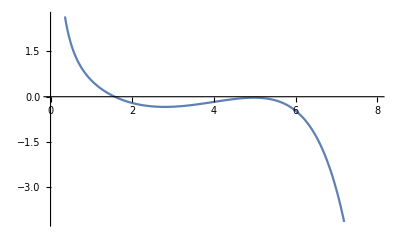

```mathematica
Series[Cos[x]/x,{x,0,10}]
Plot[Evaluate[Normal[1/x-x/2+x^3/24-x^5/720+x^7/40320-x^9/3628800+O[x]^11]],{x,0,8}]
```

## First Order Difference

## Forward Difference

### Functions Definition

```mathematica
FD[f_,S_,s_,order_,n_]:=CoefficientList[(-TS[f,S,s,order,n]+f[Subscript[x,S]]),Δx][[1]]/Δx+Simplify[(-TS[f,S,s,order,n]+f[Subscript[x,S]]-CoefficientList[(-TS[f,S,s,order,n]+f[Subscript[x,S]]),Δx][[1]])/Δx+ DT[f,S,s,order,n]]+O[Δx]^order
```

### Examples

```mathematica
f'[Subscript[x, i]]==FD[f,i+1,i,3,Δx]
```

f'[x_i]==(-f[x_i]+f[x_(1+i)])/Δx-1/2 f''[x_i] Δx-1/6 f^(3)[x_i] Δx^2+O[Δx]^3

## Backward Difference

### Functions Definition

```mathematica
BD[f_,S_,s_,order_,n_]:=CoefficientList[(TS[f, S, s, order, n] - f[Subscript[x, S]]), Δx][[1]]/Δx + Simplify[(TS[f, S, s, order, n] - f[Subscript[x, S]] - CoefficientList[(TS[f, S, s, order, n] - f[Subscript[x, S]]), Δx][[1]])/Δx - 
   DT[f, S, s, order, n]] + O[Δx]^order
```

### Examples

```mathematica
f'[Subscript[x, i]]==BD[f,i-1,i,3,-Δx]
```

f'[x_i]==(-f[x_(-1+i)]+f[x_i])/Δx+1/2 f''[x_i] Δx-1/6 f^(3)[x_i] Δx^2+O[Δx]^3

## Central Difference

### Functions Definition

```mathematica
CD[f_,SF_,SB_,s_,order_,n_]:=((f[Subscript[x,SF]]-f[Subscript[x,SB]])-(TS[f,SF,s,order,n]-TS[f,SB,s,order,-n]))/2/Δx+DT[f, SF, s, order, n]+ O[Δx]^(order+1)
```

### Examples

```mathematica
f'[Subscript[x, i]]==CD[f,i+1,i-1,i,3,Δx]
```

f'[x_i]==(-f[x_(-1+i)]+f[x_(1+i)])/(2 Δx)-1/6 f^(3)[x_i] Δx^2+O[Δx]^4

## Second Order Difference

## Forward Difference

```mathematica
FDS[f_,S_,s_,order_,n_]:=Simplify[((f'[Subscript[x, S+1]]-2*f'[Subscript[x, S]])-(TS[f,S+1,s,order,2*n]-2*TS[f,S,s,order,n]))/((Δx)^2)]+f''[Subscript[x, s]]+O[Δx]
```

### Examples

```mathematica
f''[Subscript[x, i]]==FDS[f,i+1,i,2,Δx]
```

f''[x_i]==(f[x_i]-2 f'[x_(1+i)]+f'[x_(2+i)])/Δx^2+O[Δx]^1

## Backward Difference

```mathematica
BDS[f_,S_,s_,order_,n_]:=Simplify[((f'[Subscript[x, S-1]]-2*f'[Subscript[x, S]])-(TS[f,S-1,s,order,2*n]-2*TS[f,S,s,order,n]))/((Δx)^2)]+f''[Subscript[x,s]]+O[Δx]
```

### Examples

```mathematica
f''[Subscript[x, i]]==BDS[f,i-1,i,2,-Δx]
```

f''[x_i]==(f[x_i]+f'[x_(-2+i)]-2 f'[x_(-1+i)])/Δx^2+O[Δx]^1

## Central Difference

```mathematica
CDS[f_,SF_,SB_,s_,order_,n_]:=Simplify[((f'[Subscript[x, SF]]+f'[Subscript[x, SB]])-(TS[f,SF,s,order,n]+TS[f,SB,s,order,-n]))/(Δx)^2]+f''[Subscript[x,s]]+O[Δx]^2
```

### Examples

```mathematica
CDS[f,i+1,i-1,i,2,Δx]
```

(-2 f[x_i]+f'[x_(-1+i)]+f'[x_(1+i)])/Δx^2+O[Δx]^2